## Loading Averages Files

```mathematica
Clear[RAWDATA, QUARK, GLUON]
SetDirectory[NotebookDirectory[]]
RAWDATA["Pythia"]= Drop[Import["../Pythia-8205/averages.dat", "Table"],2];
RAWDATA["Vincia"]= Drop[Import["../Vincia-1201/averages.dat", "Table"],2];
RAWDATA["Sherpa"]= Drop[Import["../Sherpa-2.1.1/averages.dat", "Table"],2];
RAWDATA["Herwig"]= Drop[Import["../Herwig-2_7_1/averages.dat", "Table"],2];
RAWDATA["Ariadne"]= Drop[Import["../Ariadne/averages.dat", "Table"],2];

ExtractQuarkShift[{Q_, R0_, β_, avguuparton_,avgggparton_, avguuhadron_, avggghadron_}]:= {Q,R0,β,4/3,(avguuhadron-avguuparton)}
ExtractGluonShift[{Q_, R0_, β_, avguuparton_,avgggparton_, avguuhadron_, avggghadron_}]:= {Q,R0,β,3,(avggghadron-avgggparton)}

QUARK[type_]:= QUARK[type] = ExtractQuarkShift/@RAWDATA[type]
GLUON[type_]:= GLUON[type] = ExtractGluonShift/@RAWDATA[type]

LOGIFY[{Q_, R0_, β_,Ci_, value_}]:= {Q,R0, β, Ci, Log[Max[value, 10^-5]] }

MCs = {"Pythia", "Vincia", "Sherpa", "Herwig", "Ariadne"};

RAWDATA["All"] = Flatten[Join[RAWDATA[#]&/@MCs],1];
```

/Users/jthaler/outside/lh2015-qg/AnalyticResum

## Performing Fit

```mathematica
βone =0.9999999;
FORM[Q_, R0_, β_, Ω0_,Ξ0_, Ci_] :=(1/(β  -βone)((Ci* Ω0)/(Q/2 *R0))(1- ((Ci* Ξ0)/(Q/2 *R0))^(β-βone )));

QUARKANS = FindFit[LOGIFY/@QUARK["All"],{Log[Max[FORM[Q, R0, β, Ω0,Ξ0,Ci], 10^-5]],3>Ω0>0.1,3>Ξ0>0.1} , {Ω0,Ξ0} , {Q, R0,β,Ci}]
GLUONANS = FindFit[LOGIFY/@GLUON["All"],{Log[Max[FORM[Q, R0, β, Ω0,Ξ0,Ci], 10^-5]],2>Ω0>0.1,2>Ξ0>0.1} , {Ω0,Ξ0} , {Q, R0,β,Ci}]
COMBOANS =  FindFit[LOGIFY/@Join[QUARK["All"],GLUON["All"]],{Log[Max[FORM[Q, R0, β, Ω0,Ξ0,Ci], 10^-5]],3>Ω0>0.1,3>Ξ0>0.1} , {Ω0,Ξ0} , {Q, R0,β,Ci}]
```

{Ω0→0.272495,Ξ0→0.433186}

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{Ω0→0.14921,Ξ0→0.238713}

{Ω0→0.205025,Ξ0→0.336429}

```mathematica
QUARKANSnocas = FindFit[LOGIFY/@QUARK["All"],{Log[Max[FORM[Q, R0, β, Ω0,Ξ0,1], 10^-5]],3>Ω0>0.1,3>Ξ0>0.1} , {Ω0,Ξ0} , {Q, R0,β,Ci}]
GLUONANSnocas = FindFit[LOGIFY/@GLUON["All"],{Log[Max[FORM[Q, R0, β, Ω0,Ξ0,1], 10^-5]],2>Ω0>0.1,2>Ξ0>0.1} , {Ω0,Ξ0} , {Q, R0,β,Ci}]
COMBOANSnocas =  FindFit[LOGIFY/@Join[QUARK["All"],GLUON["All"]],{Log[Max[FORM[Q, R0, β, Ω0,Ξ0,1], 10^-5]],3>Ω0>0.1,3>Ξ0>0.1} , {Ω0,Ξ0} , {Q, R0,β,Ci}]
```

{Ω0→0.36351,Ξ0→0.578624}

{Ω0→0.447278,Ξ0→0.714192}

{Ω0→0.403152,Ξ0→0.64303}

### Alternative Version with just Omega0

```mathematica
(*βone =0.9999999;
FORM[Q_, R0_, β_, Ω0_,Ξ0_, Ci_] :=(1/(β  -βone)((Ci* Ω0)/(Q/2 *R0))(1- ((Ci* Ξ0)/(Q/2 *R0))^(β-βone )));

QUARKANS = FindFit[LOGIFY/@QUARK["All"],{Log[Max[FORM[Q, R0, β, Ω0,Ω0,Ci], 10^-5]],3>Ω0>0.1} , {Ω0} , {Q, R0,β,Ci}]
GLUONANS = FindFit[LOGIFY/@GLUON["All"],{Log[Max[FORM[Q, R0, β, Ω0,Ω0,Ci], 10^-5]],2>Ω0>0.1} , {Ω0} , {Q, R0,β,Ci}]
COMBOANS =  FindFit[LOGIFY/@Join[QUARK["All"],GLUON["All"]],{Log[Max[FORM[Q, R0, β, Ω0,Ω0,Ci], 10^-5]],2>Ω0>0.1} , {Ω0} , {Q, R0,β,Ci}]*)
```

```mathematica
(*QUARKANSnocas = FindFit[LOGIFY/@QUARK["All"],{Log[Max[FORM[Q, R0, β, Ω0,Ω0,1], 10^-5]],3>Ω0>0.1} , {Ω0} , {Q, R0,β,Ci}]
GLUONANSnocas = FindFit[LOGIFY/@GLUON["All"],{Log[Max[FORM[Q, R0, β, Ω0,Ω0,1], 10^-5]],2>Ω0>0.1} , {Ω0} , {Q, R0,β,Ci}]
COMBOANSnocas =  FindFit[LOGIFY/@Join[QUARK["All"],GLUON["All"]],{Log[Max[FORM[Q, R0, β, Ω0,Ω0,1], 10^-5]],3>Ω0>0.1} , {Ω0} , {Q, R0,β,Ci}]*)
```

## Creating Minimum/Maximum List

```mathematica
(*Assumes identical formatting!*)

QUARK["MinMax"]= Table[
{QUARK["Pythia"][[i,1]],
QUARK["Pythia"][[i,2]],
QUARK["Pythia"][[i,3]],
QUARK["Pythia"][[i,4]],
Min[QUARK[#][[i,5]]& /@ MCs ],
Max[QUARK[#][[i,5]]& /@ MCs ]
}
, {i,1,Length[QUARK["Pythia"]]}];

GLUON["MinMax"]= Table[
{GLUON["Pythia"][[i,1]],
GLUON["Pythia"][[i,2]],
GLUON["Pythia"][[i,3]],
GLUON["Pythia"][[i,4]],
Min[GLUON[#][[i,5]]& /@ MCs ],
Max[GLUON[#][[i,5]]& /@ MCs ]
}
, {i,1,Length[QUARK["Pythia"]]}];
```

## Plotting Shifts

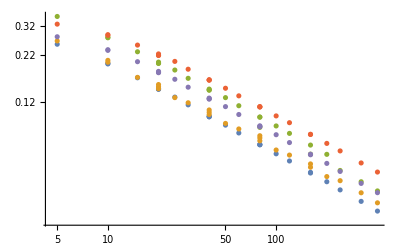

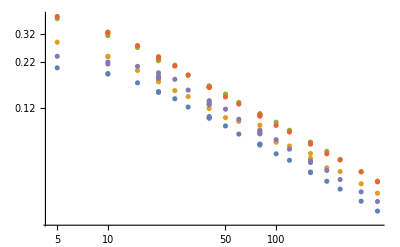

```mathematica
CHOOSE[beta_,list_]:= Select[list, (#[[3]] ==beta)&]
GETQR[{Q_, R0_, β_ ,CA_, shift_}]:= {Q/2 * R0, shift}
ISOLATEQR[beta_,list_]:=Sort[GETQR/@ CHOOSE[beta,list],( #1[[1]] >  #2[[1]] )&]

ListLogLogPlot[ISOLATEQR[0.5,QUARK[#]]&/@ MCs]
ListLogLogPlot[ISOLATEQR[0.5,GLUON[#]]&/@ MCs]
```

## Band Plots

{ImageSize→20,AspectRatio→0.5,BaselinePosition→Scaled[0.1]}

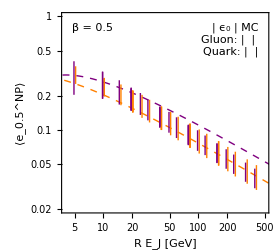

../tex_jhep/figures/npshift_05.pdf

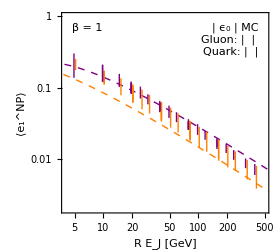

../tex_jhep/figures/npshift_10.pdf

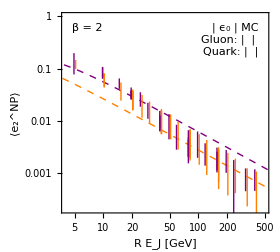

../tex_jhep/figures/npshift_20.pdf

```mathematica
Clear[BANDDEF,ANALYTIC]
BANDDEF[off_][{Q_, R0_, β_ ,CA_, min_, max_}]:= Line[{{Log[Q/2 * R0]+off,Log[Max[ min, 10^-4] ]},{Log[Q/2 * R0]+off, Log[max]}}]

QUARKBANDS[beta_]:=BANDDEF[0.02]/@ CHOOSE[beta, QUARK["MinMax"]]
GLUONBANDS[beta_]:=BANDDEF[-0.02]/@ CHOOSE[beta, GLUON["MinMax"]]

RANGEMIN[0.5]= 0.02;
RANGEMIN[1]= 0.002;
RANGEMIN[2]= 0.0002;

RANGEMAX[0.5]= 1.0;
RANGEMAX[1]= 1.0;
RANGEMAX[2]= 1.0;

lineoptions = {ImageSize->20,AspectRatio->0.5,BaselinePosition->Scaled[.1]}

ANALYTIC[beta_] := LogLogPlot[{
FORM[2 EJ, 1,beta, Ω0,Ξ0, 4/3]/. COMBOANS,
FORM[2 EJ, 1, beta,Ω0,Ξ0, 3]/. COMBOANS
(*,
FORM[2 EJ, 1, beta,Ω0,Ξ0, 1]/. COMBOANSnocas*)
}
, {EJ,2,800}, PlotRange -> {{4,500}, {RANGEMIN[beta],RANGEMAX[beta]}}, Frame->True,BaseStyle -> {FontFamily->"Times",14}, TicksStyle -> Thickness[Medium], FrameStyle -> Thickness[Medium], PlotTheme-> "Classic", LabelStyle ->  {FontFamily->"Times", Black}, AspectRatio -> 0.9,
FrameLabel-> {R "E_J [GeV]",⟨Subscript[e, beta]^(NP)⟩}, RotateLabel -> False, PlotStyle -> {Directive[Orange, Dashed], Directive[Purple,Dashed],  Directive[Black,Dashed]},
ImageSize -> 280,
 Epilog-> {Inset[Column[{
Style[StandardForm[Text[Style["β = " <>ToString[beta], Bold]]]]}],Scaled[{0.05,0.95}],{Left,Top}]
,
Directive[FontFamily->"Times",FontSize-> 12],
Inset[Grid[Identity[{{Style[""],Style["ϵ_0"],Style["MC"], Style["{Ω_0,Ξ_0}/GeV"]},{Style["Quark:",Orange],Graphics[{Orange,Dashed,Thickness[Medium],Line[{{-0.5,0},{0.5,0}}]},lineoptions],Graphics[{Orange,Thickness[Large],Line[{{0,-0.5},{0,0.5}}]},lineoptions],
Style[{Round[Ω0 * 4/3 /. COMBOANS, 0.01],Round[Ξ0* 4/3 /. COMBOANS, 0.01]}]
},
{Style["Gluon:", Purple],Graphics[{Purple,Dashed,Thickness[Medium],Line[{{-0.5,0},{0.5,0}}]},lineoptions],Graphics[{Purple,Thickness[Large],Line[{{0,-0.5},{0,0.5}}]},lineoptions],
Style[{Round[Ω0 * 3 /. COMBOANS, 0.01],Round[Ξ0* 3 /. COMBOANS, 0.01]}]
},
{Style["No C_i:", Black],Graphics[{Black,Dashed,Thickness[Medium],Line[{{-0.5,0},{0.5,0}}]},lineoptions],"",
Style[{Round[Ω0 * 3 /. COMBOANSnocas, 0.01],Round[Ξ0* 3 /. COMBOANSnocas, 0.01]}]
}
}[[{1,3,2}, {1,2,3}]]], Spacings->{0.5,0.1}
],Scaled[{0.95,0.95}],{Right,Top}]
}
];

MYPLOT[beta_]:= Show[ANALYTIC[beta], Graphics[{Orange, Thickness[Large],QUARKBANDS[beta], Purple, GLUONBANDS[beta]}]]

MYPLOT[0.5]
Export["../tex_jhep/figures/npshift_05.pdf",%]
MYPLOT[1]
Export["../tex_jhep/figures/npshift_10.pdf", %]
MYPLOT[2]
Export["../tex_jhep/figures/npshift_20.pdf", %]
```

## Testing Integral

```mathematica
Integrate[1/z 1/θ z θ^β,  {z,nt,1}, {θ,Min[nt/z, z],1}, Assumptions -> {1/2>nt >0}]
(%/. nt ->Ξ0)- (%/. nt -> Ξ0-Ω0)//FullSimplify
Series[%, {Ω0,0,1}]//Simplify
```

-(1-nt-nt^β+nt^(1+β)+2 nt^(1/2+β/2) β-nt^β β-nt^(1+β) β-β^2+nt β^2)/((-1+β) β (1+β))

(Ξ0^β+β Ξ0^β-2 β Ξ0^((1+β)/2)-Ξ0^(1+β)+β Ξ0^(1+β)+2 β (Ξ0-Ω0)^((1+β)/2)+Ω0-β^2 Ω0-(Ξ0-Ω0)^β (1-Ξ0+β (1+Ξ0-Ω0)+Ω0))/(β (-1+β^2))

((Ξ0-β Ξ0+β Ξ0^β-β Ξ0^((1+β)/2)+(-1+β) Ξ0^(1+β)) Ω0)/((-1+β) β Ξ0)+O[Ω0]^2

```mathematica
Plot[(nt^β-(n nt)^β-nt β+n nt β)/(β-β^2)1/δ/. nt -> 0.1 /. δ -> {3,0.1,0.01,0.001, 0.00001}, {β,0,2}]
```

-Graphics-

```mathematica
Simplify[(-Ξ0^β+β (Ξ0-Ω0)+Ω0^β)/((-1+β) β)/. Ω0 -> 0, β>0]
```

(β Ξ0-Ξ0^β)/((-1+β) β)

```mathematica
(-Ξ0^β+β (Ξ0-Ω0)+Ω0^β)/((-1+β) β)
```

(-Ξ0^β+β (Ξ0-Ω0)+Ω0^β)/((-1+β) β)

```mathematica
Series[(β Ξ0-Ξ0^β)/((-1+β) β), {β,1,0}]
```

(Ξ0-Ξ0 Log[Ξ0])+O[β-1]^1

```mathematica
((Ξ0-β Ξ0+β Ξ0^β-β Ξ0^((1+β)/2)+(-1+β) Ξ0^(1+β)) Ω0)/((-1+β) β Ξ0)
Series[%, {β,1,1}]
```

((Ξ0-β Ξ0+β Ξ0^β-β Ξ0^((1+β)/2)+(-1+β) Ξ0^(1+β)) Ω0)/((-1+β) β Ξ0)

(-Ω0+Ξ0 Ω0+1/2 Ω0 Log[Ξ0])+(Ω0-Ξ0 Ω0+Ξ0 Ω0 Log[Ξ0]+3/8 Ω0 Log[Ξ0]^2) (β-1)+O[β-1]^2